# Network Map Animation Routines

## Functions

```mathematica
<<PajaroLocoPublic`
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,2;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Black]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->15,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]
BarChartPopCountsFrames[subsetPopulations_,{colors_,maxPop_,frameDimensions_}]:=BarChart[subsetPopulations[[All,1;;(Length[labels]-1)]],
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{.5,Length[subsetPopulations]+.5},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->.2,
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Top,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_}]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->{0,0},
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Bottom,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
]
ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
White,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+1*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+1*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.01],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
AspectRatio->Automatic,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
CalculateNetworkParameters[cities_,transitionsMatrix_]:=Module[{range,transitionsMatrix2,vertexCoordinates,transMatrix},
range=Range[cities//Length];
transitionsMatrix2={transitionsMatrix,ToString/@range};
vertexCoordinates=cities;
transMatrix={ReplacePart[Chop[transitionsMatrix2[[1]]//UpperTriangularize],{i_,i_}->0],transitionsMatrix2[[2]]};
{range,transMatrix,vertexCoordinates}
]
CalculateVertexScalers[{range_,nodeScaler_},scaledSizesPieChartFramesAtFrame_]:=Module[{vertexShapes,vertexSizes},
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2,1]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->nodeScaler*#[[2,2]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
{vertexShapes,vertexSizes}
]
GenerateNetworkFrames[vertexShapeAndSizeFrames_,{vertexCoordinates_,networkMatrix_},{edgeThreshold_,lineThickness_,frameDimensions_},countryMap_,colorPalette_]:=Module[{},
GraphTransitionsFrequenciesWithMax[networkMatrix,edgeThreshold,
VertexCoordinates->vertexCoordinates,
LineThickness->lineThickness,
VertexShape->vertexShapeAndSizeFrames[[1]],
VertexSize->vertexShapeAndSizeFrames[[2]],
VariableStyle->"LineColor",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->frameDimensions[[1]],
Prolog->
{
EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[.35],colorPalette[[1]],
countryMap[[2]],
EdgeForm[Directive[Opacity[1],Thickness[.05],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]],
countryMap[[2]],
EdgeForm[Directive[Opacity[.35],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]],
countryMap[[1]]
},
ImagePadding->200
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]

GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Directive[Black,Thickness[.15]]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed",ImagePadding->4],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
```

```mathematica
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={1,{#[[1]],#[[2]]},50}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[1;;All]];
{cities,transitionsMatrix}
]
```

```mathematica
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
Sigmoid[x_]:=.5+1/(1+ⅇ^(-5x+1.75))
```

```mathematica
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{
ImageRotate[barChart,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&,
(*dayCount//ImageRotate[Show[#],90Degree]&,*)
network//Show[#,ImageSize->(ImageDimensions[#])]&,
(*popCount//Show[#]&*),
ImageRotate[flow,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&
}}];
Rasterize[row]
]
```

## Load Data

```mathematica
(*Set the path for the experiments*)
USER=2;
return=If[USER==1,SetDirectory["/Users/sanchez.hmsc/Desktop/SplitDrive/"],1];
return=If[USER==2,SetDirectory["/Users/sanchez.hmsc/Desktop/LinkedDrive/"],1];
(*Subset datasets to export a specific set of frames*)
framesRange={1,4250};
(*User-Defined data range for frames, and aesthetic parameters*)
(*genotypesIndicesToAggregate={
{"H*",{5,6,7,12,15,16,17,22,25,26,27}},
{"Other",{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30}}
};*)
genotypesIndicesToAggregate={
{"Hx",{2,5,6,7}},
{"RR",{8}},
{"Other",{1,3,4,9,10}}
};
(**)
{frameDimensions,scaler,resolution,colorScheme,nodeScaler}={{2560,1440},3.5,500,"LakeColors",1.5};
(*Import data and calculate necessary values*)
{{maleDatasets,femaleDatasets},{genotypes,ticksMax,{maleMax,femaleMax}}}=ImportAndReshapeMosquitoDatasets["./E_02_11_00020/",{"ADM_Mean","AF1_Mean"}];
```

```mathematica
{outputFolder,outputBarCharts,outputFlow,outputNetworks,outputPopCounts,outputFullFrames}={"./Frames","/BarCharts/","/Flow/","/Networks/","/PopCounts/","/FullFrames/"};
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks,baseFullFrames}={"PopCount","DayCount","BarCharts","Flow","Networks","FullFrame"};
{Range[Length[genotypes]],genotypes}//Transpose
(*Aggregate dataset*)
totalPopulationDatasets=(maleDatasets+femaleDatasets);
{aggregatedLabels,aggregatedPopulations}=AggregatePopulationByGenotypeIndices[totalPopulationDatasets,genotypesIndicesToAggregate];
aggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[aggregatedPopulations];
{labels,colors}=GenerateColorPalette[aggregatedLabels,colorScheme];
maxPop=aggregatedPopulationsAcrossNodes[[All,Length[labels]]]//Max;
```

{{1,WW},{2,WH},{3,WR},{4,WB},{5,HH},{6,HR},{7,HB},{8,RR},{9,RB},{10,BB}}

```mathematica
originalColorsValues={
{30,45,0,10},
{0,15,20,0},
{10,10,10,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
colors=rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Transpose[{rgbColors,genotypesIndicesToAggregate}]//Grid;
maxPopSize=aggregatedPopulationsAcrossNodes//Flatten//Max;
SwatchLegend[rgbColors,genotypesIndicesToAggregate[[All,1]]
,LabelStyle->30
,LegendMarkerSize->25
]
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Export["./frames/"<>"00_ColorSwatch.png",%%,ImageResolution->500];
```

```mathematica
colors
```

{RGBColor[0.63, 0.495, 0.9],RGBColor[1., 0.85, 0.8],RGBColor[0.9, 0.9, 0.9]}

Generate Blank Transitions Matrix

```mathematica
citiesNumber=maleDatasets//Length;
transitionsMatrix=ConstantArray[0,{citiesNumber,citiesNumber}];
scaledTransitionsMatrix=1*(ⅇ^(1000#)-1)&/@ReplacePart[transitionsMatrix,{i_,i_}->0];
meanTransitions=scaledTransitionsMatrix//Flatten//Mean;
networkMatrix=Chop/@UpperTriangularize[scaledTransitionsMatrix];
networkMatrixThreshold=Table[If[#>meanTransitions/1.25,#,0]&/@i,{i,networkMatrix}];
```

Cluster Cities

```mathematica
rawCities=Import["KM_coordinates.csv"][[2;;All]];
{coords,pops}={rawCities[[All,1;;2]],rawCities[[All,3]]};
```

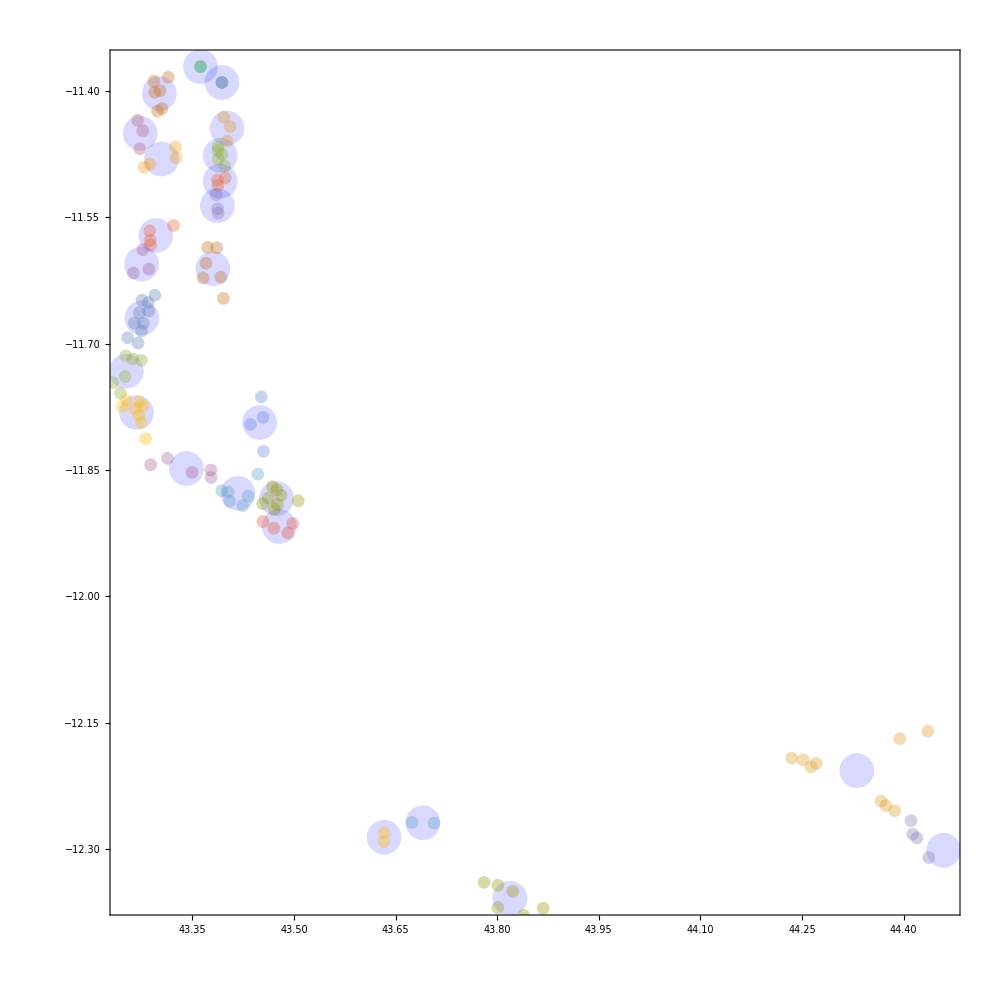

ComorosClusters.pdf

```mathematica
(*{SEED,CLUSTERS}={42,25};
SeedRandom[SEED]
clustersNumber=CLUSTERS;
clusters=FindClusters[coords ,clustersNumber, Method->"KMeans"];*)

clusters={{{43.2543044,-11.6931255},{43.2717536,-11.6633441},{43.2777104,-11.6759846},{43.2748593,-11.685177},{43.285342,-11.6614195},{43.2845126,-11.6513186},{43.2945036,-11.6428324},{43.2755297,-11.648627},{43.2697992,-11.6993776},{43.2641798,-11.6757211}},{{44.3942831,-12.168846},{44.3665058,-12.2427614},{44.3738095,-12.2481055},{44.3868488,-12.2542262},{44.4357152,-12.1599178},{44.2346362,-12.1916668},{44.2513425,-12.1938521},{44.2631736,-12.2021585},{44.2708162,-12.1979978}},{{43.274666,-11.7199316},{43.2504262,-11.7390992},{43.2621745,-11.7184486},{43.2321538,-11.7462387},{43.2436335,-11.7589678},{43.2514089,-11.7145432}},{{43.3220221,-11.5600257},{43.2881193,-11.5831413},{43.2867484,-11.5664557},{43.2873857,-11.5775436}},{{44.4371606,-12.3098998},{44.5063393,-12.3764349},{44.5263641,-12.2753593},{44.4195781,-12.2865703},{44.4135321,-12.2820255},{44.4106854,-12.2659801},{44.4994958,-12.3121605}},{{43.2930126,-11.3888547},{43.3022349,-11.4001499},{43.2941378,-11.4020466},{43.3050624,-11.4212636},{43.2983679,-11.4242569},{43.3141286,-11.3840893}},{{43.674034,-12.2680605},{43.7064096,-12.268939}},{{43.6330827,-12.280605},{43.6328045,-12.2908374}},{{43.3770624,-11.8499805},{43.3495099,-11.8528894},{43.3131564,-11.8362673},{43.3774739,-11.8589411},{43.288311,-11.8438376}},{{43.4807388,-11.8800784},{43.5062231,-11.8865711},{43.4536995,-11.8900801},{43.4755418,-11.8910295},{43.4705912,-11.8964094},{43.468004,-11.8697282},{43.4748452,-11.8734286},{43.4620521,-11.8833369}},{{43.4540567,-11.911239},{43.4979651,-11.9135062},{43.490771,-11.9247875},{43.4701705,-11.9190778}},{{43.4356978,-11.795945},{43.4542626,-11.7877563},{43.4515954,-11.7632851},{43.4548201,-11.8278645}},{{43.2872361,-11.4870208},{43.2787077,-11.4910236},{43.3249831,-11.4669826},{43.3259914,-11.4796887}},{{43.2724769,-11.4690325},{43.276791,-11.44765},{43.2690474,-11.4351724}},{{43.3618274,-11.3715503}},{{43.3934696,-11.3902679}},{{43.3960288,-11.4314198},{43.4056931,-11.4424736},{43.4013507,-11.4596896}},{{43.3878065,-11.4667285},{43.387745,-11.470978},{43.3878083,-11.4811466},{43.393797,-11.4754035},{43.3976859,-11.4895819}},{{43.3868104,-11.5059996},{43.3874836,-11.512427},{43.3984576,-11.5035445}},{{43.3877436,-11.5455356},{43.3871962,-11.5400807},{43.3851737,-11.5234957}},{{43.3918662,-11.6213561},{43.3956701,-11.6464791},{43.3858439,-11.5864172},{43.3655926,-11.6222256},{43.3722602,-11.5860109},{43.3700067,-11.604797}},{{43.4464571,-11.8549783},{43.4242587,-11.8923212},{43.3932323,-11.8746048},{43.4027092,-11.8762117},{43.4321459,-11.8808683},{43.4048261,-11.8869569}},{{43.2523717,-11.7671406},{43.2462882,-11.7747038},{43.2649358,-11.7777033},{43.2772945,-11.7741939},{43.2719588,-11.769172},{43.2708659,-11.7855211},{43.2743263,-11.793823},{43.2810122,-11.8129215}},{{43.2857562,-11.6117233},{43.262706,-11.6164592},{43.2766194,-11.588576}},{{43.8009302,-12.369111},{43.800803,-12.3427047},{43.7805116,-12.3392664},{43.8678657,-12.3698839},{43.8389949,-12.3783584},{43.8229488,-12.3497985}}};
clustersCentroids={Mean[#[[All,1]]],Mean[#[[All,2]]]}&/@clusters;
clustersIndices=Table[Flatten[Position[coords,#]&/@i],{i,clusters}];
clusteredPopulations=Table[Total[pops[[#]]&/@i],{i,clustersIndices}];
(**)
original=ListPlot[
clusters
,PlotStyle->Directive[Opacity[.35]]
];
clustersRender=ListPlot[clustersCentroids
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,PlotStyle->Directive[PointSize[.025],Blue,Opacity[.15]]
];
Show[{clustersRender,original},ImageSize->1000]
Export["ComorosClusters.pdf",%]
```

Process Coordinates

```mathematica
{xOffset,yOffset}={0,-.075};
latLongs=clustersCentroids;
populations=clusteredPopulations;
(**)
ordering=Range[latLongs//Length];(*(Reverse/@latLongs)//Ordering//Reverse*)
latLongs={latLongs[[ordering]][[All,1]]+xOffset,latLongs[[ordering]][[All,2]]+yOffset}//Transpose;
populations=populations[[ordering]]
(**)
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
minMaxes={Min[#],Max[#]}&/@(latLongs//Transpose);
center=Mean/@minMaxes;
gridSize=Max[Abs[(#[[1]]-#[[2]])]&/@minMaxes]*.6;
```

{2273318,411,1209771,27771,352,3529,9,5829,33016,642,1238,6679,84,36,56,1345,4236,41087,31382,20544,152070,821,29286,40206,6}

Generate Map

{CMYKColor[Rational[7, 10], Rational[1, 2], 0, 0],CMYKColor[0, Rational[3, 4], Rational[1, 2], 0],CMYKColor[0, 0, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

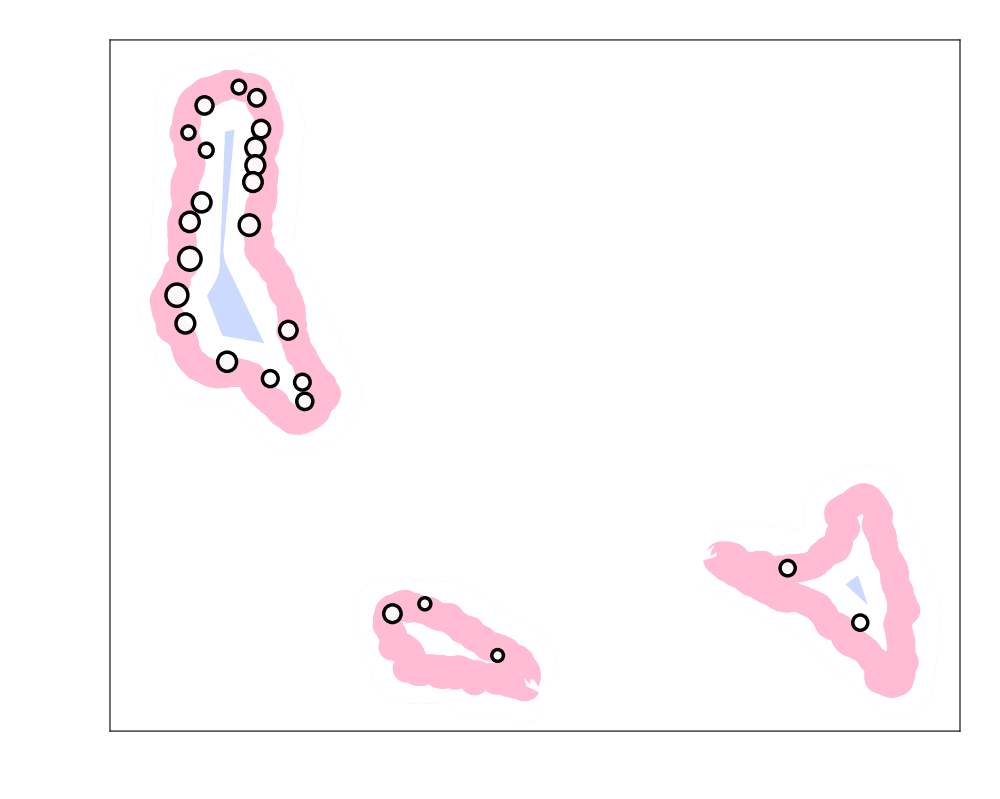

Comoros.pdf

```mathematica
countryName="Comoros";
originalColorsValuesMap={
{70,50,0,0},
{0,75,50,0},
{0,0,0,0},
{100,100,100,100},
{0,0,0,0}
};
(**)
mapPolygons={countryPolygon,countrySchematicPolygon}={CountryData[countryName,"Polygon"],CountryData[countryName,"SchematicPolygon"]};
colorPaletteMap=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValuesMap
mapRender=GeoGraphics[{
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPaletteMap[[5]],.06]]],Opacity[.35],colorPaletteMap[[1]]],
mapPolygons[[2]],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],colorPaletteMap[[5]]]],Opacity[.2],colorPaletteMap[[3]]],
mapPolygons[[2]],
GeoStyling[EdgeForm[Directive[Opacity[.35],Thickness[.020],colorPaletteMap[[2]]]],Opacity[0],colorPaletteMap[[5]]],
mapPolygons[[1]]
}
,AspectRatio->Automatic
,Axes->False
,Frame->True
,FrameStyle->Directive[colorPaletteMap[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashing[.0025],Thickness[.00075],colorPaletteMap[[4]]}]
,ImageSize->1000
(*,PlotRange->({#-gridSize,#+gridSize}&/@center)*)
,GeoBackground->None
,Prolog->{colorPaletteMap[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPaletteMap[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.0025],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],Log[1+0.01+#[[2]]/200]]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[0],
Text[
Style[countryName,100,Lighter[colorPaletteMap[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.25gridSize,center[[2]]+gridSize*.25}]
}
]
Export["Comoros.pdf",mapRender]
```

Aggregate Counts With GeoClusters

```mathematica
clusteredAggregatedPopulations=Table[Total[aggregatedPopulations[[#]]&/@i],{i,clustersIndices}][[ordering]];
clusteredAggregatedPopulations=Map[Round,clusteredAggregatedPopulations,Infinity];
```

## Generate Rasters

Flow Chart (only needs to be run once)

```mathematica
barChartPopDynFrames=Map[
BarChartPopDynamicsFrames[#,aggregatedPopulationsAcrossNodes,{colors,maxPopSize,framesRange[[2]],frameDimensions,labels}]&,
{framesRange[[2]]}
];
Export[outputFolder<>"/Flow/"<>"FlowFull.png",barChartPopDynFrames,ImageResolution->300,ImageSize->frameDimensions[[1]]]
```

./Frames/Flow/FlowFull.png

Population Counts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
popCountsFrames=GeneratePopCountsFrames[{labels,colors},subsetPopulationsAccrossNodes];
(*popCountGridFrames=Grid[{{#[[1]]},{},{},{#[[2]]}}]&/@Transpose[{dayCounter,popCountsFrames}];*)
ExportFrames[popCountsFrames,dataRange,{outputFolder,outputPopCounts,baseCounts}];
dayCounterFrames=Style[("Day: "<>StringPadLeft[ToString[#],5,"0"]),50]&/@Range[dataRange[[1]],dataRange[[2]]];
ExportFrames[dayCounterFrames,dataRange,{outputFolder,outputPopCounts,baseDays}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,dayCounterFrames,popCountsFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Bar Charts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
barChartFrames=ParallelMap[
BarChartPopCountsFrames[#,{colors,Ceiling[maleMax+femaleMax],frameDimensions}]&,
subsetPopulations
];
ExportFrames[barChartFrames,dataRange,{outputFolder,outputBarCharts,baseBarCharts}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Population Dynamics

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fullRaster=Import[outputFolder<>outputFlow<>"FlowFull.png"];
days=Range[dataRange[[1]],dataRange[[2]]];
barChartPopDynMaskedFrames=ParallelMap[BarChartPopDynamicsMaskFrames[fullRaster,{#,framesRange[[2]]}]&,days];
ExportFrames[barChartPopDynMaskedFrames,dataRange,{outputFolder,outputFlow,basePopDyn}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartPopDynMaskedFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Map

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
subsetPopulations=SubsetPopulations[{clusteredAggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
pieChartFrames=ParallelMap[GeneratePieChartsAtTick[#,labels,maleMax+femaleMax]&,subsetPopulations[[1]]];
pieChartFrames=Table[{#[[1]],Sigmoid[#[[2]]]}&/@i,{i,pieChartFrames}];
{range,networkMatrix,vertexCoordinates}=CalculateNetworkParameters[latLongs,transitionsMatrix];
vertexShapeAndSizeFrames=ParallelMap[CalculateVertexScalers[{range,nodeScaler*1.05},#]&,pieChartFrames];
networkFrames=ParallelTable[
GenerateNetworkFrames[vertexShapeAndSizeFrames[[j]],{{#[[1]],#[[2]]+.075}&/@vertexCoordinates,networkMatrix},{1,.0001,frameDimensions},mapPolygons,colorPaletteMap]
,{j,1,stepSize+1}];
ExportFrames[networkFrames,dataRange,{outputFolder,outputNetworks,baseNetworks}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,pieChartFrames,vertexShapeAndSizeFrames,networkFrames,range,networkMatrix,vertexCoordinates];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Map Debug

{{{{0,0,9.95964×10^6,9.95964×10^6},{0,0,1887.4,1887.4},{0,0,5.29985×10^6,5.29985×10^6},{0,0,121660.,121660.},{0,0,1582.6,1582.6},{0,0,15521.6,15521.6},{0,0,56.8,56.8},{0,0,25715.2,25715.2},{553.4,12382.4,131325.,144261.},{58.,2763.4,0,2821.4},{2685.,248.2,0,2933.2},{1637.4,26025.2,0,27662.6},{0,0,444.6,444.6},{0,0,199.6,199.6},{0,0,265.8,265.8},{0,0,5881.8,5881.8},{0,0,18707.,18707.},{0,0,179897.,179897.},{0,0,138209.,138209.},{0,0,89471.,89471.},{0,0,666120.,666120.},{699.2,2366.8,0,3066.},{0,0,128471.,128471.},{0,0,176183.,176183.},{0,0,133.2,133.2}},{{0,0,9.95939×10^6,9.95939×10^6},{0,0,1891.8,1891.8},{0,0,5.2996×10^6,5.2996×10^6},{0,0,121678.,121678.},{0,0,1577.,1577.},{0,0,15460.6,15460.6},{0,0,58,58},{0,0,25734.4,25734.4},{542.4,12399.6,131320.,144262.},{59.6,2762.,0,2821.6},{2677.4,245.,0,2922.4},{1632.4,26042.8,0,27675.2},{0,0,446.4,446.4},{0,0,194.4,194.4},{0,0,264,264},{0,0,5857.6,5857.6},{0,0,18743.8,18743.8},{0,0,180017.,180017.},{0,0,138231.,138231.},{0,0,89561.8,89561.8},{0,0,666175.,666175.},{701.8,2350.8,0,3052.6},{0,0,128619.,128619.},{0,0,176231.,176231.},{0,0,137.2,137.2}},{{0,0,9.95838×10^6,9.95838×10^6},{0,0,1885.4,1885.4},{0,0,5.2995×10^6,5.2995×10^6},{0,0,121702.,121702.},{0,0,1585.2,1585.2},{0,0,15446.6,15446.6},{0,0,58.6,58.6},{0,0,25723.2,25723.2},{528.6,12434.8,131344.,144308.},{58.8,2769.6,0,2828.4},{2690.6,244.8,0,2935.4},{1613.2,26071.4,0,27684.6},{0,0,441.6,441.6},{0,0,194.4,194.4},{0,0,262.4,262.4},{0,0,5823.6,5823.6},{0,0,18745.4,18745.4},{0,0,179967.,179967.},{0,0,138258.,138258.},{0,0,89529.8,89529.8},{0,0,666091.,666091.},{695.,2349.4,0,3044.4},{0,0,128681.,128681.},{0,0,176403.,176403.},{0,0,139.2,139.2}},{{0,0,9.95858×10^6,9.95858×10^6},{0,0,1883.4,1883.4},{0,0,5.29941×10^6,5.29941×10^6},{0,0,121637.,121637.},{0,0,1595.2,1595.2},{0,0,15464.,15464.},{0,0,60.8,60.8},{0,0,25674.,25674.},{528.6,12444.4,131347.,144320.},{59.,2764.2,0,2823.2},{2704.6,247.6,0,2952.2},{1619.6,26076.,0,27695.6},{0,0,438.8,438.8},{0,0,196.,196.},{0,0,261.4,261.4},{0,0,5824.4,5824.4},{0,0,18704.,18704.},{0,0,180031.,180031.},{0,0,138113.,138113.},{0,0,89570.2,89570.2},{0,0,666125.,666125.},{691.8,2342.4,0,3034.2},{0,0,128651.,128651.},{0,0,176421.,176421.},{0,0,141.4,141.4}},{{0,0,9.95794×10^6,9.95794×10^6},{0,0,1882.4,1882.4},{0,0,5.29932×10^6,5.29932×10^6},{0,0,121593.,121593.},{0,0,1601.8,1601.8},{0,0,15482.,15482.},{0,0,60.6,60.6},{0,0,25600.8,25600.8},{520.8,12441.8,131297.,144260.},{58.,2749.4,0,2807.4},{2702.2,247.4,0,2949.6},{1627.6,26092.4,0,27720.},{0,0,442.4,442.4},{0,0,195.8,195.8},{0,0,257.4,257.4},{0,0,5826.6,5826.6},{0,0,18692.2,18692.2},{0,0,180013.,180013.},{0,0,137987.,137987.},{0,0,89580.2,89580.2},{0,0,666212.,666212.},{689.8,2356.8,0,3046.6},{0,0,128598.,128598.},{0,0,176338.,176338.},{0,0,139.8,139.8}}},{{5633.,43786.,1.69612×10^7,1.70106×10^7},{5613.6,43800.2,1.69612×10^7,1.70106×10^7},{5586.2,43870.,1.69602×10^7,1.70096×10^7},{5603.6,43874.6,1.69601×10^7,1.70096×10^7},{5598.4,43887.8,1.69591×10^7,1.70085×10^7}}}

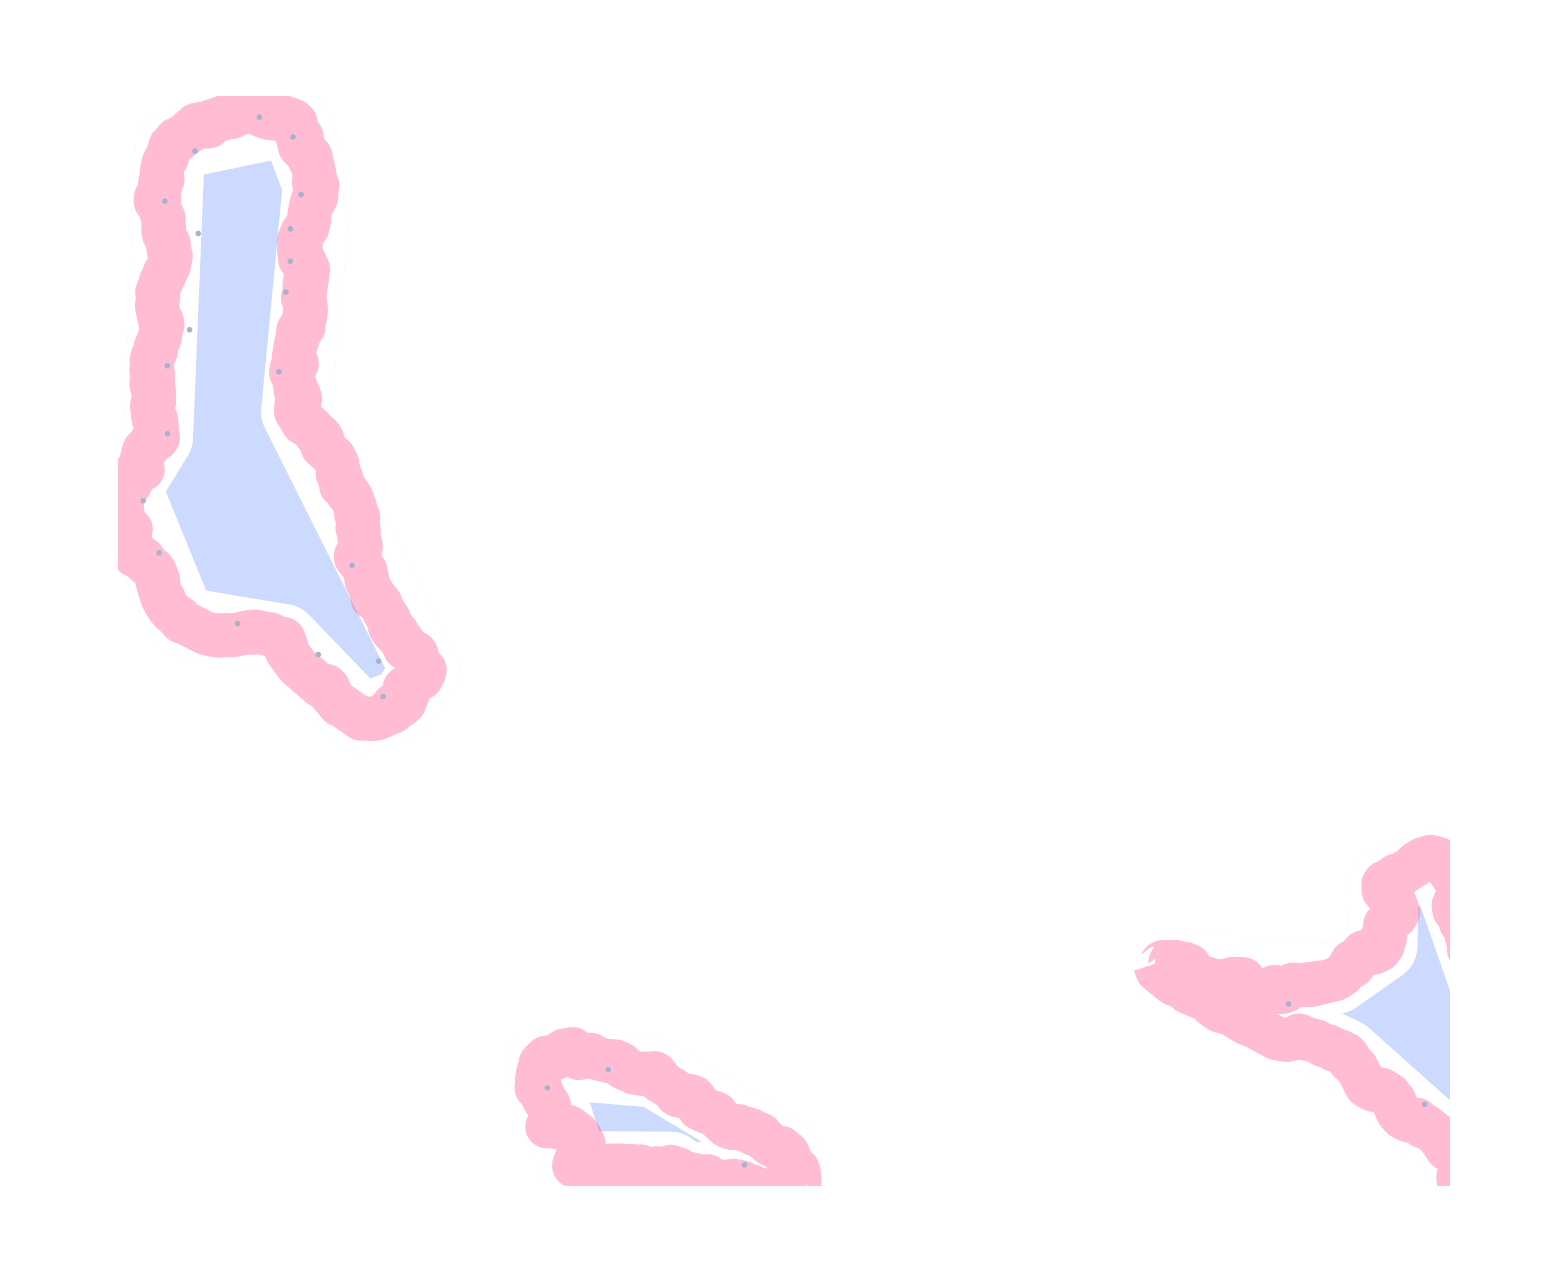
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=2000;
stepSize=4;
(*Subset Data*)
dataRange={i,i+stepSize};
subsetPopulations=SubsetPopulations[{clusteredAggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange]
pieChartFrames=ParallelMap[GeneratePieChartsAtTick[#,labels,maleMax+femaleMax]&,subsetPopulations[[1]]];
pieChartFrames=(Table[{#[[1]],Sigmoid[#[[2]]]}&/@i,{i,pieChartFrames}]);
{range,networkMatrix,vertexCoordinates}=CalculateNetworkParameters[latLongs,transitionsMatrix];
vertexShapeAndSizeFrames=ParallelMap[CalculateVertexScalers[{range,nodeScaler*1.05},#]&,pieChartFrames];
networkFrames=ParallelTable[
GenerateNetworkFrames[vertexShapeAndSizeFrames[[j]],{{#[[1]],#[[2]]+.075}&/@vertexCoordinates,networkMatrix},{1,.0001,frameDimensions},mapPolygons,colorPaletteMap]
,{j,1,stepSize+1}]
```

## Final Frames

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fileNames=ParseFilenames[#,
{
outputFolder,
{outputPopCounts,outputBarCharts,outputFlow,outputNetworks},
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks}
}]&/@Range[dataRange[[1]],dataRange[[2]]];
fullFrames=ParallelMap[GenerateAnimationFrameFromFiles[#]&,fileNames];
ExportFrames[fullFrames,dataRange,{outputFolder,outputFullFrames,baseFullFrames}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,fileNames,fullFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```